{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl,surface11.gpl,surface12.gpl,surface13.gpl,surface14.gpl,surface15.gpl,surface16.gpl,surface17.gpl,surface18.gpl,surface19.gpl,surface20.gpl,surface21.gpl,surface22.gpl,surface23.gpl,surface24.gpl,surface25.gpl,surface26.gpl,surface27.gpl,surface28.gpl,surface29.gpl,surface30.gpl,surface31.gpl,surface32.gpl,surface33.gpl,surface34.gpl,surface35.gpl,surface36.gpl,surface37.gpl,surface38.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion

{{50,9379.61},{75,8802.83},{100,8684.75},{125,8996.9},{150,8931.39},{175,10782.3},{200,9173.01},{225,9453.09},{250,9483.66},{275,9707.12},{300,17949.3},{325,10437.7},{350,58712.6},{375,11964.3},{400,10192.3},{425,10100.7},{450,10212.7},{475,10281.1},{500,10377.8},{525,13585.7},{550,12184.6},{575,10911.5},{600,13414.6},{625,10848.7},{650,10983.6},{675,11111.1},{700,11436.9},{725,11324.1},{750,21771.3},{775,13978.7},{800,14373.8},{825,32481.8},{850,14051.3},{875,3.05564×10^7},{900,18218.5},{925,11640.6},{950,12612.8},{975,12433.5},{1000,70539.4}}

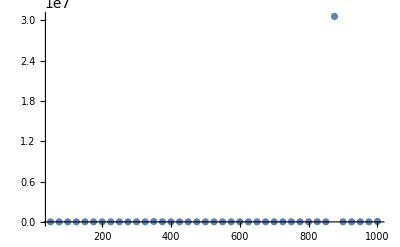

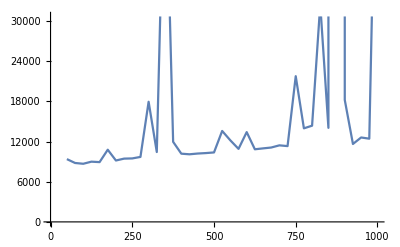

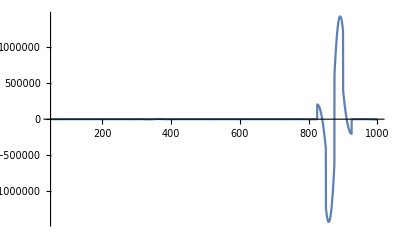

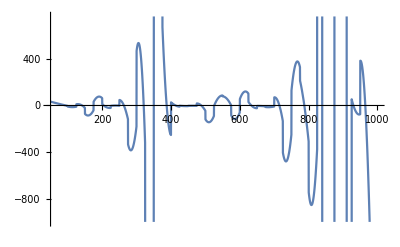

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange -> All];
{plot1,plot2}
]
files= FileNames[];
(*Print[files]*)
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"]
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
energysepfunc = Interpolation[SolveForce["energysep.txt"]];
forcefunction = energysepfunc';
ListPlot[SolveForce["energysep.txt"], PlotRange->All]
ListPlot[allData,Joined->True]
Plot[-1*(forcefunction[x]), {x, 50, 1000}, PlotRange->All]
force[x_]=-D[Interpolation[allData,InterpolationOrder->3][x],x];
Plot[force[x],{x,50, 1000}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```